# CARBAPENEM RESISTANCE MODEL

## Data

### Preparing Directory

Clear all variables. Set directory and change setting such that when it closes it closes all outputs.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]}];
```

### Load Data

Reading country data on consumption and resistance and assigning them to appropriate variables.

```mathematica
countryname="US_DDD"; 
data=Import["DataSheet_cddep.xlsx",{"Data",countryname}];
data = data[[All,2;;]];
years = data[[1]];
tt = Length[years]; 
nop = (Length[data]-5)/2; (*# of pathogens*)
isolates = data[[2;;Length[data]-4;;2]];
resistance = data[[3;;Length[data]-4;;2]];
rfreq =resistance/isolates;
carbcons =  data[[-1]];
conbreak = data[[-3,1;;nop]]; (*CBP consumption for KP, PA, AB*)
cbp =data[[-2,1]]*Table[carbcons*conbreak[[i]],{i,1,nop}];
```

## Model

### Parameters & Model Structure

r(t) = frequency of resistance
k_s= natural growth rate of the sensitive strain
k_r= natural growth rate of the resistance strain (k_r < k_s)
θ = k_r-k_s< 0 
a = CBP consumption (DDD)

```mathematica
r[t_,r0_,ks_,θ_]:=ⅇ^(Total[ks*a[[1;;t]]]+θ*t)/((1/r0)-1+ⅇ^(Total[ks*a[[1;;t]]]+ θ*t));
```

### Likelihood

```mathematica
Lik[r0_,ks_,θ_]:= Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,θ]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,θ]],{j,1,tt}]]
```

```mathematica
(*Likelihood Surface
i = 3;
iso = isolates[[i]]
resis = resistance[[i]]
a = cbp[[i]]
loglik[r0_,ks_]:=Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,-0.1]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,-0.1]],{j,1,tt}]]
Plot3D[loglik[r0,ks],{r0,0,0.1},{ks,700,1000}]*)
```

### Model Fitting

```mathematica
max  = PadRight[{},nop,Null];
fr0 = max; fks=max; fθ=max;
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],{max[[i]],{fr0[[i]],fks[[i]],fθ[[i]]}}=NMaximize[{Lik[r0,ks,θ],0<r0<1,θ<-0.1},{r0,ks,θ}, MaxIterations->100000]}]

fr0 = Table[fr0[[i]][[2]],{i,1,nop}];
fks = Table[fks[[i]][[2]],{i,1,nop}] ;
fθ=Table[fθ[[i]][[2]],{i,1,nop}];

(*create table of fitted values*)
params= Join[{max},{fr0},{fks},{fθ}];
headings1=Prepend[params,{"KP","PA","AB","EA/C"}];
headings2=MapThread[Prepend,{headings1,{"","Likelihood","r0","k_s","θ"}}];
Grid[headings2,Frame-> All]
```

| KP | PA | AB | EA/C
Likelihood | -338.471 | -120.611 | -160.27 | -113.668
r0 | 0.00618264 | 0.187208 | 0.171297 | 0.000773001
k_s | 112.653 | 24.2885 | 127.527 | 223.918
θ | -0.1 | -0.1 | -0.1 | -0.1

```mathematica
Sampling
```

Sampling

```mathematica
loglik[r0_,ks_]:=Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,-0.1]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,-0.1]],{j,1,tt}]];
fonGrid[x_,y_,f_]:=Module[{n,m,fvals},
(*x is an n-by-1 vector*)
(*y is an n-by-1 vector*)
(*f is a scalar function of two variables*)
(*fvals is an m-by-n matirx where fVals[[i,j]]=f[x[[j]],y[[i]]]*)
n=Length[x];
m=Length[y];
fvals=Table[0,{m},{n}];(*preallocate fvals*)Do[Do[fvals[[i,j]]=f[x[[j]],y[[i]]];,{i,1,m}];,{j,1,n}];
fvals]
```

```mathematica
r0f  = PadRight[{},nop,Null];ksf  = PadRight[{},nop,Null];lf  = PadRight[{},nop,Null];
pn = 4;(*PATHOGEN NO*)
i = pn; 
iso = isolates[[i]];
resis = resistance[[i]];
a = cbp[[i]];
x = RandomReal[{0.9*fr0[[i]],1.1*fr0[[i]]},100];
y = RandomReal[{0.9*fks[[i]],1.1*fks[[i]]},100];
ld = fonGrid[x,y,loglik];
d = Exp[ld];
w = d/Total[Total[d]];
ds =ArrayReshape[d,{1,100*100}][[1]];
ws = ArrayReshape[w,{1,100*100}][[1]];
repeat[m_,n_Integer?Positive]:=Sequence@@ConstantArray[m,n]
xs = Table[repeat[x[[i]],100],{i,1,100}];
ys = PadRight[y,10000,y];
rs = RandomChoice[ws->Range[10000],1000];
r0f[[i]] = xs[[rs]]; ys = ys[[rs]]; ds = ds[[rs]];
ksf[[i]]=ys;lf[[i]]=ds;
```

```mathematica
od = Ordering[ds];
xs = xs[[od]]; ys=ys[[od]];
xss =xs[[50;;1000]];yss=ys[[50;;1000]];
```

#### Plots

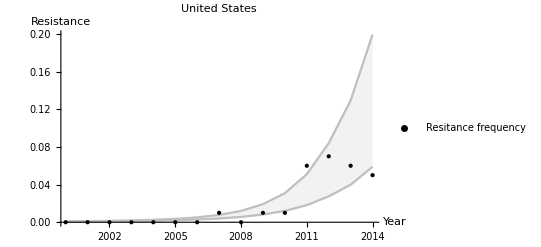

```mathematica
t=Range[1,tt]; 
nos = 951;
i =pn;
xp =PadRight[{},nos,Null];
res = Transpose@{years,rfreq[[i]]}; (*resistance frequency data*)
For[j=1,j≤nos,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],xp[[j]]= Table[r[k,xss[[j]],yss[[j]],-0.1],{k,1,tt}]}];
xpt = Transpose[xp]; 
xpm = Table[Min[xpt[[r]]],{r,1,Length[years]}]; xpM = Table[Max[xpt[[r]]],{r,1,15}];
xpv = {xpm,xpM};
fit = Table[Transpose@{years,xpv[[i]]},{i,1,2}];
plotD = ListPlot[res,PlotStyle->{{Black,PointSize[Large]}},PlotRange->All,PlotLegends->{"Resitance frequency"}];
plotM =ListLinePlot[Table[fit[[j]],{j,2}],PlotStyle->RGBColor[0.75,0.75,0.75],AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->"Model fit",Filling->{1->{2}}];
Show[{plotM,plotD},PlotRange->All]
```

## Projections

### Status Quo & Interventions

```mathematica
cbp0 = data[[-2,1]]*carbcons[[-1]];  (*current CBP consumption*)
ti=years[[-1]]; (*projectsion begin at year Subscript[t, i]*)
tf =2030; (*projection until year Subscript[t, f]*) 
nyears = tf -ti;(*# of years to project across*)
pyears = Range[ years[[-1]],tf];
```

```mathematica
(*Status Quo: maintain current CBP consumption*)
projSQ =ConstantArray[cbp0,Round[nyears]];
cbpSQ = Table[Join[cbp[[i]],projSQ*conbreak[[i]]],{i,1,nop}];
(*Interventions:
   (0) sparing1: 0 consumption at Subscript[t, i] 
  (1) sparing2: linear reduction to 0 consumption by Subscript[t, f]
(2) stewardship1: immediate reduction to a % of current consumption
(3) stewardship2: linear reduction to the a % of current consumption *) 

intv = 0.4; (*reduce current carbapenem consumption by (1-intv) % in next npy years linearly*)
option = 1; (*select 0-3; see above*)

If[option==0, projI = ConstantArray[0,Round[nyears]], 
If[option==1,projI = Range[cbp0,0,(-1)*cbp0/(nyears-1)], 
If[option==2, projI=ConstantArray[intv*cbp0,Round[nyears]], 
If[option == 3, projI = Range[cbp0,intv*cbp0,cbp0*(intv-1)/(nyears-1)]]]]];
cbpI = Table[Join[cbp[[i]], projI*conbreak[[i]]],{i,1,nop}];
```

```mathematica
t=Range[1,tt]; 
i =pn; 
res = Transpose@{years,rfreq[[i]]}; (*resistance frequency data*)
xsq =PadRight[{},nos,Null];
For[j=1,j≤nos,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpSQ[[i]],xsq[[j]]= Table[r[k,xss[[j]],yss[[j]],-0.1],{k,tt,tt+nyears}]}];
xsqt = Transpose[xsq]; 
xsqm = Table[Min[xsqt[[r]]],{r,1,Length[pyears]}]; xsqM = Table[Max[xsqt[[r]]],{r,1,Length[pyears]}];
xsqv = {xsqm,xsqM};
xfp =PadRight[{},nos,Null];
For[j=1,j≤nos,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpI[[i]],xfp[[j]]= Table[r[k,xss[[j]],yss[[j]],-0.1],{k,tt,tt+nyears}]}];
xfpt = Transpose[xfp]; 
xfpm = Table[Min[xfpt[[r]]],{r,1,Length[pyears]}]; xfpM = Table[Max[xfpt[[r]]],{r,1,Length[pyears]}];
xfpv = {xfpm,xfpM};
fitS = Table[Transpose@{pyears,xsqv[[i]]},{i,1,2}];
fitP = Table[Transpose@{pyears,xfpv[[i]]},{i,1,2}];
```

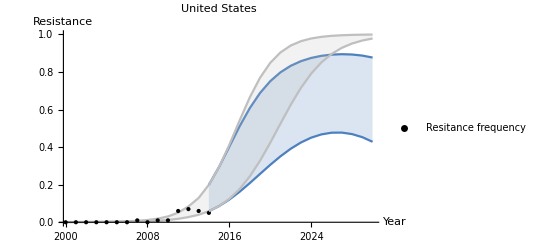

```mathematica
plotS =ListLinePlot[Table[fitS[[j]],{j,2}],PlotStyle->{RGBColor[0.75,0.75,0.75]},AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",Filling->{1->{2}}];
plotP =ListLinePlot[Table[fitP[[j]],{j,2}],PlotStyle->RGBColor[0.3,0.5,0.75],AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",Filling->{1->{2}}];
Show[{plotM,plotD,plotP,plotS},PlotRange->All]
```